### Mass Matrix - 1 Flavour Scenario for Next to Nearest Neighbour Clockwork

```mathematica
K = 25;qt=0;a=1;q=-1;q1=-1.0;
(* qt is q^∼ (Majorana mass term), K is the number of sites and a is mass term (m) and q and q1 are the neighbouring and next to nearest neighbour coupling strength term in CW fermions. *)
```

```mathematica
ncw= Table[0,{x,2K+1},{y,2K+1}];
(* Dummy matrix to form clockwork mass matrix *)
```

```mathematica
i=1;While[i<2K+2,{ncw[[i,i]] = qt };i++]
i=1;While[i<K+1,{ncw[[i,K+i]] = a};i++]
i=1;While[i<K+1,{ncw[[K+i,i]] = a };i++]
i=1;While[i<K+1,{ncw[[i,K+1+i]] = q};i++]
i=1;While[i<K+1,{ncw[[K+1+i,i]] = q};i++]
i=1;While[i<K,{ncw[[i,K+2+i]] = q1};i++]
i=1;While[i<K,{ncw[[K+2+i,i]] = q1};i++]
(* Clockwork mass matrix in Ψ basis, where Ψ = ( Subscript[ψ, L,0],Subscript[ψ, L,1],Subscript[ψ, L,2], ..... Subscript[ψ, L,K-1],Subscript[ψ^c, R,0],Subscript[ψ^c, R,1], .... Subscript[ψ^c, R,K] *)
```

```mathematica
ns =NullSpace[N[ncw,30]]
```

(1.11022×10^-16 | 1.94289×10^-16 | 1.52656×10^-16 | 2.77556×10^-17 | -1.38778×10^-16 | -7.45931×10^-17 | 3.72966×10^-17 | 5.33427×10^-17 | 6.32737×10^-17 | -7.41548×10^-17 | 4.72163×10^-17 | 4.2628×10^-17 | 4.012×10^-16 | 2.15044×10^-17 | -6.53144×10^-18 | -2.82392×10^-18 | -1.91104×10^-16 | 7.5699×10^-18 | -6.49834×10^-17 | 3.24792×10^-17 | -1.98225×10^-16 | -7.78709×10^-17 | -6.46646×10^-17 | -8.64646×10^-17 | 7.63259×10^-17 | 0.786151 | 0.485868 | 0.300283 | 0.185585 | 0.114698 | 0.0708872 | 0.0438107 | 0.0270765 | 0.0167342 | 0.0103423 | 0.0063919 | 0.00395041 | 0.00244148 | 0.00150893 | 0.000932556 | 0.000576372 | 0.000356185 | 0.000220187 | 0.000135998 | 0.0000841891 | 0.0000518087 | 0.0000323804 | 0.0000194283 | 0.0000129522 | 6.47608×10^-6 | 6.47608×10^-6)

```mathematica
Kcw = ncw[[1;;K,K+1;;2K+1]]
```

(1 | -1 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -1 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | -1 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | -1 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | -1 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | -1 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1.
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1)

```mathematica
{s1,s2,s3}=SingularValueDecomposition[N[Kcw,30]];
```

```mathematica
NullSpace[N[Kcw,30]]
```

(-0.786151 | -0.485868 | -0.300283 | -0.185585 | -0.114698 | -0.0708872 | -0.0438107 | -0.0270765 | -0.0167342 | -0.0103423 | -0.0063919 | -0.00395041 | -0.00244148 | -0.00150893 | -0.000932556 | -0.000576372 | -0.000356185 | -0.000220187 | -0.000135998 | -0.0000841891 | -0.0000518087 | -0.0000323804 | -0.0000194283 | -0.0000129522 | -6.47608×10^-6 | -6.47608×10^-6)

```mathematica
ev = Eigenvalues[N[ncw,30]] (*Eigenvalue upto precision of 30 significant digits.*)
```

{-2.22398,2.22398,2.22303,-2.22303,2.18798,-2.18798,2.18424,-2.18424,-2.12887,2.12887,-2.12062,2.12062,-2.048,2.048,-2.03375,2.03375,1.94735,-1.94735,1.92593,-1.92593,1.82956,-1.82956,1.8003,-1.8003,1.69815,-1.69815,-1.661,1.661,-1.55769,1.55769,-1.51354,1.51354,1.41421,-1.41421,-1.36524,1.36524,1.27574,-1.27574,-1.22596,1.22596,1.15283,-1.15283,-1.10864,1.10864,-1.05859,1.05859,1.02865,-1.02865,-1.00674,1.00674,5.7727×10^-16}

```mathematica
Y = Eigenvectors[N[ncw,30]];
```

```mathematica
H= Inverse[Y];
```

```mathematica
Ev1 = Sort[Abs[ ev]];
```

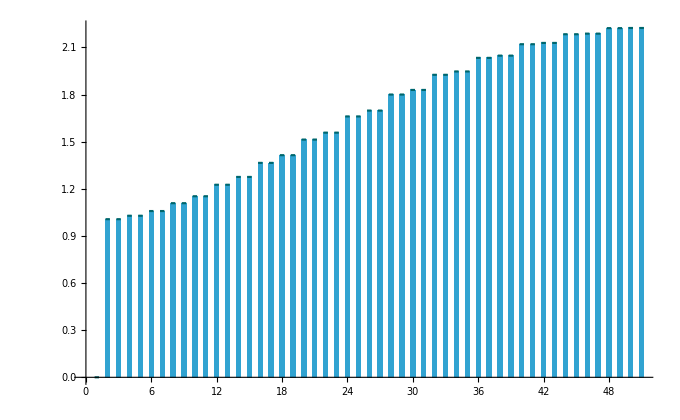

```mathematica
DiscretePlot[Ev1⟦i⟧,{i,1,2 K+1},PlotStyle->Directive[RGBColor[0.,0.4,0.42],Opacity[1.],AbsoluteThickness[1.545]],ExtentSize->0.4,ImageSize->680,BaseStyle->{FontFamily->"LM Roman 10",FontSize->10},Filling->Axis,FillingStyle->Opacity[0.9,RGBColor[0.1,0.6,0.8]],FrameTicks->{Automatic,Automatic},FrameLabel->{"n","M(TeV)"},LabelStyle->Directive[Bold,Medium],PlotRange->{0,All}, Epilog->{Text[ "",Scaled[{0.8,0.95}]],Text["",Scaled[{0.8,0.9}]]}]
```

```mathematica
Rn = H[[2K+1,All]] (* Coupling to muon*)
(* Change of basis from Subscript[ψ^c, R,r]  to eigenvector of cw2 in interaction term. *)
```

{-0.0142072,-0.0142072,-0.0298575,-0.0298575,-0.0286866,0.0286866,-0.0590095,0.0590095,-0.0437256,0.0437256,-0.0867281,-0.0867281,0.0596423,-0.0596423,-0.112234,-0.112234,0.0768006,0.0768006,-0.13465,-0.13465,0.0956211,-0.0956211,0.152935,0.152935,0.116578,0.116578,-0.16576,0.16576,-0.14015,0.14015,-0.171338,-0.171338,0.166667,-0.166667,-0.167191,0.167191,-0.195891,0.195891,-0.150019,0.150019,0.226166,-0.226166,-0.11626,-0.11626,-0.253196,0.253196,0.0645257,-0.0645257,0.269886,0.269886,6.47608×10^-6}

```mathematica
srn = s3[[-1]] (*0-Mode Components*)
```

{0.020092,-0.0422249,0.0405689,-0.083452,0.0618373,-0.122652,0.084347,-0.158722,0.108612,0.190424,0.135229,0.216282,0.164866,-0.23442,0.198202,0.242309,0.235702,-0.236443,0.277032,-0.212159,0.319847,0.164417,-0.358073,0.0912531,0.381677,-6.47608×10^-6}

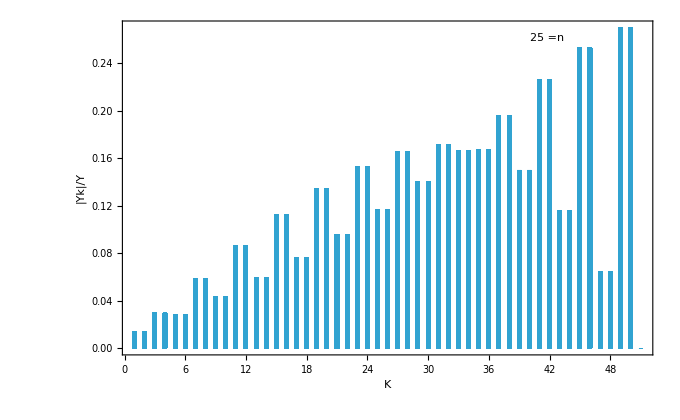

```mathematica
DiscretePlot[Abs[Rn[[i]]],{i,1,2*K+1},ExtentSize->0.4,ImageSize->680,BaseStyle->{FontFamily->"LM Roman 10",FontSize->10},Frame->True,PlotStyle-> {Opacity[0.9,RGBColor[0.1,.6,.8]],Directive[AbsoluteThickness[0]]},
Filling->Axis,FillingStyle->Opacity[0.9,RGBColor[0.1,.6,.8]],FrameTicks->{Automatic,Automatic},FrameLabel->{"K","|Yk|/Y"},LabelStyle->Directive[Bold, Medium],Epilog->{Text["",Scaled[{0.8,0.90}]],Text["",Scaled[{0.8,0.95}]],{Text[K"=n",Scaled[{.8,.95}]]}}]
```

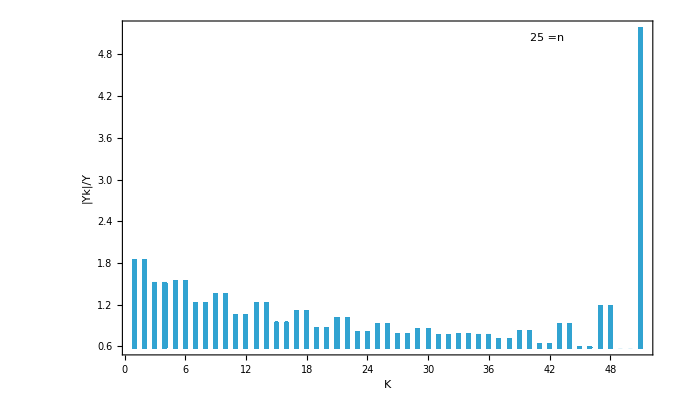

```mathematica
DiscretePlot[Abs[Log10[Abs[Rn[[i]]]]],{i,1,2*K+1},ExtentSize->0.4,ImageSize->680,BaseStyle->{FontFamily->"LM Roman 10",FontSize->10},Frame->True,PlotStyle-> {Opacity[0.9,RGBColor[0.1,.6,.8]],Directive[AbsoluteThickness[0]]},
Filling->Axis,FillingStyle->Opacity[0.9,RGBColor[0.1,.6,.8]],FrameTicks->{Automatic,Automatic},FrameLabel->{"K","|Yk|/Y"},LabelStyle->Directive[Bold, Medium],PlotRange->All,Epilog->{Text["",Scaled[{0.8,0.90}]],Text["",Scaled[{0.8,0.95}]],{Text[K"=n",Scaled[{.8,.95}]]}}]
```

```mathematica
Lvector = Transpose[s1];(*Left Eigenvector of NNNCW*)
Rvector= Transpose[s3];(*Right Eigenvector of NNNCW*)
```

```mathematica
Lvector[[-1]]
```

{-0.0446842,0.,-0.0887641,-7.00443×10^-16,-0.131644,-3.04801×10^-17,-0.172743,-8.24048×10^-16,-0.211506,-2.0686×10^-16,-0.247409,-6.4028×10^-16,-0.279966,3.111×10^-17,-0.308737,-1.4243×10^-16,-0.333333,3.83004×10^-16,-0.353422,1.4008×10^-16,-0.36873,0.,-0.379053,0.,-0.384249}

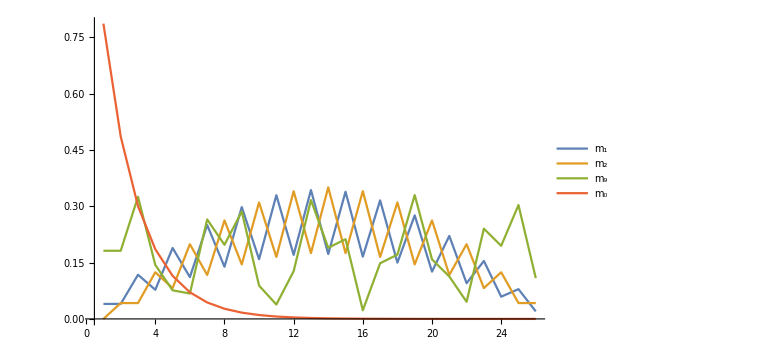
-Graphics-Absolute value of eigenvector componentsSite

```mathematica
Labeled[Labeled[ListLinePlot[{Abs[Rvector[[1]]],Abs[Rvector[[2]]],Abs[Rvector[[9]]],Abs[Rvector[[-1]]]},PlotRange->All,PlotLegends->Placed[LineLegend[ColorData[97]/@Range[Length[Rvector]],(*Explicit colors*){"\!\(\*SubscriptBox[\(m\), \(1\)]\)","\!\(\*SubscriptBox[\(m\), \(2\)]\)","\!\(\*SubscriptBox[\(m\), \(9\)]\)","\!\(\*SubscriptBox[\(m\), \(0\)]\)"}]//Framed[#,FrameStyle->Black,RoundingRadius->5,Background->White]&,Right],AxesLabel->{None,None},PlotRange->All,ImageSize->Large,PlotStyle->ColorData[97]/@Range[Length[Rvector]]],Style[Rotate["Absolute value of eigenvector components",90 Degree],14],Left],Style["Site",14],Bottom]
```

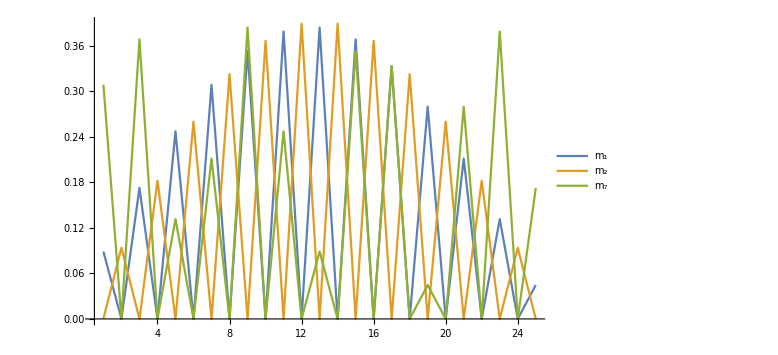
-Graphics-Absolute value of eigenvector componentsSite

```mathematica
Labeled[Labeled[ListLinePlot[{Abs[Lvector[[1]]],Abs[Lvector[[2]]],Abs[Lvector[[7]]]},PlotRange->All,PlotLegends->Placed[LineLegend[ColorData[97]/@Range[Length[Rvector]],(*Explicit colors*){"\!\(\*SubscriptBox[\(m\), \(1\)]\)","\!\(\*SubscriptBox[\(m\), \(2\)]\)","\!\(\*SubscriptBox[\(m\), \(7\)]\)"}]//Framed[#,FrameStyle->Black,RoundingRadius->5,Background->White]&,Right],AxesLabel->{None,None},PlotRange->All,ImageSize->Large,PlotStyle->ColorData[97]/@Range[Length[Rvector]]],Style[Rotate["Absolute value of eigenvector components",90 Degree],14],Left],Style["Site",14],Bottom]
```

### 3 Flavour Scenario

```mathematica
q=4;K=15;q1=q;v=0.173;p=0.1*v; 
(*K is the number of sites parameter, p is the coupling strength between SM neutrino and Subscript[R, n], and q is neighbouring coupling strength and q1 next to nearest neighbour.*)
```

```mathematica
cw= Table[0,{x,K+1},{y,K+1}];
(* Dummy matrix to form clockwork mass matrix *)
```

```mathematica
i=1;
While[i<K+1,{cw[[i+1,i+1]]=1,cw[[i+1,i]]=-q};i++]
i=1;
While[i<K,{cw[[i+2,i]]=-q1};i++]
cw2=cw;cw3=cw;
(* Clockwork mass matrix in Ψ basis, where Ψ = ( Subscript[ψ, L,0],Subscript[ψ, L,1],Subscript[ψ, L,2], ..... Subscript[ψ, L,K-1],Subscript[ψ^c, R,0],Subscript[ψ^c, R,1], .... Subscript[ψ^c, R,K] *)
```

```mathematica
cw[[1,1]]=p;cw2[[1,1]]=1.01p;cw3[[1,1]]=0.6p;(*3 NNN-CW chains for 3 masses.*)
```

```mathematica
cw3
```

(0.01038 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-4 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -4 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -4 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -4 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -4 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -4 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -4 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 | -4 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 | -4 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 | -4 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 | -4 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 | -4 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 | -4 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 | -4 | 1)

```mathematica
{u1,m1,v1}=SingularValueDecomposition[SetPrecision[cw,25]];{u2,m2,v2}=SingularValueDecomposition[SetPrecision[cw2,25]];{u3,m3,v3}=SingularValueDecomposition[SetPrecision[cw3,25]];
```

```mathematica
a1=m1[[-1,-1]]
a2=m2[[-1,-1]]
a3=m3[[-1,-1]](*Three Masses produced*)
```

1.097002154051404615870741×10^-12

1.107972026240464979811835×10^-12

6.582041174807925311209057×10^-13

```mathematica
(a2^2-a1^2)*Power[10,24](*Mass squared differences Subscript[Δm^2, 21].*)
(a3^2-a2^2)*Power[10,24](*Mass squared differences Subscript[Δm^2, 32].*)
```

0.02418828493797995311202

-0.794369350662732681741735